```mathematica
f[x_] = Log[x]
```

Log[x]

```mathematica
g[x_]=D[f[x],x]
```

1/x

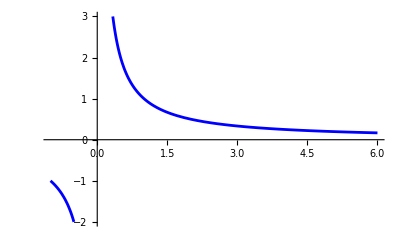

```mathematica
Plot[g[x],{x,-1,6}, PlotRange->{-2,3}, PlotStyle->Blue]
```

```mathematica
D[Log[x], x]
```

1/x

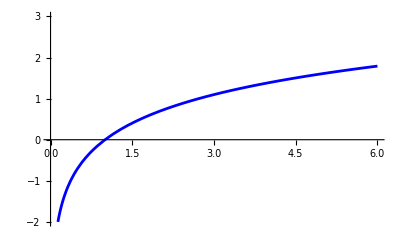

```mathematica
plot1 = Plot[f[x],{x,-1,6}, PlotRange -> {-2,3},PlotStyle ->Blue]
```

```mathematica
h[x_] = x-1
```

-1+x

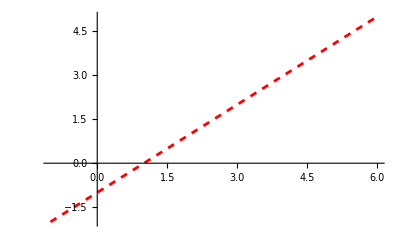

```mathematica
plot2 =Plot[tangent[x],{x,-1,6}, PlotStyle -> {Dashed,Red}]
```

```mathematica
g[x_] = x/E
```

x/ⅇ

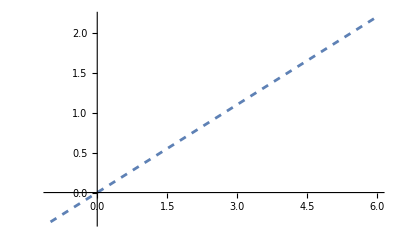

```mathematica
plot3 = Plot[tangent2[x],{x,-1,6}, PlotStyle -> {Dashed,Grey}]
```

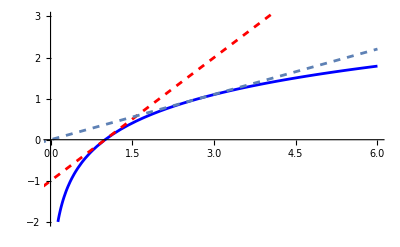

```mathematica
Show[plot1,plot2,plot3]
```

```mathematica
h[x_] = Piecewise[{{0,x<=0},{1,x>0}},{x,-2,2}]
```

Piecewise[{{0, x≤0}, {1, x>0}, {{x,-2,2}, True}}]

Piecewise[{{0, x≤0}, {1, x>0}, {{x,-2,2}, True}}]

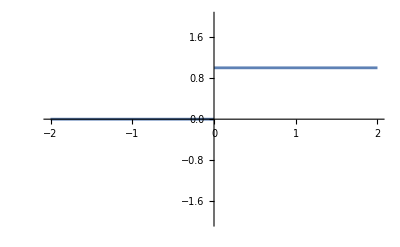

```mathematica
Piecewise[{{0, x≤0}, {1, x>0}, {{x,-2,2}, True}}]
plot4 =Plot[h[x],{x,-2,2}, PlotRange ->{-2,2}]
```

```mathematica
g[x_] =2h[x]-1
```

-1+2 (Piecewise[{{0, x≤0}, {1, x>0}, {{x,-2,2}, True}}])

-1+2 (Piecewise[{{0, x≤0}, {1, x>0}, {{x,-2,2}, True}}])

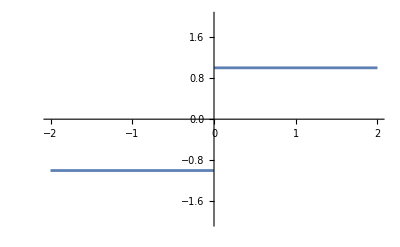

```mathematica
-1+2 (Piecewise[{{0, x≤0}, {1, x>0}, {{x,-2,2}, True}}])
plot5 = Plot[g[x],{x,-2,2},PlotRange -> {-2,2}]
```

```mathematica
Int[x_] =Integrate[g[x],x]
```

Piecewise[{{-x, x≤0}, {x, True}}]

```mathematica
Piecewise[{{-x, x≤0}, {x, True}}]
Int2[x_] = Integrate[Int[x],x]
```

Piecewise[{{-x, x≤0}, {x, True}}]

Piecewise[{{-x^2/2, x≤0}, {x^2/2, True}}]

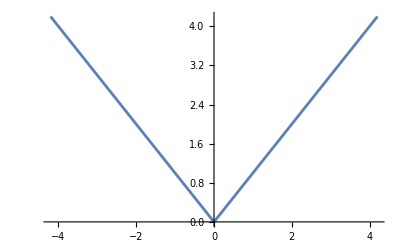

```mathematica
Plot[Piecewise[{{-x,x≤0}},x],{x,-4.2,4.2}]
```

Piecewise[{{-x^2/2, x≤0}, {x^2/2, True}}]

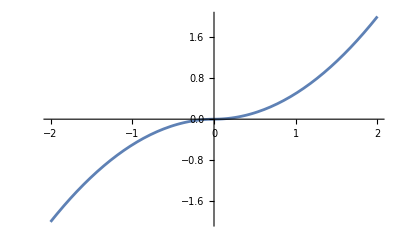

```mathematica
Piecewise[{{-x^2/2, x≤0}, {x^2/2, True}}]
plot7 = Plot[Int2[x],{x,-2,2}]
```

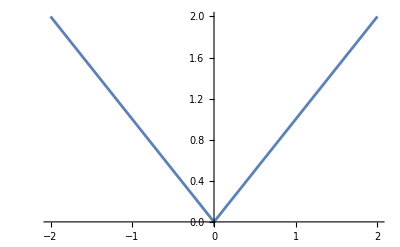

```mathematica
plot6 =Plot[Int[x],{x,-2,2}]
```

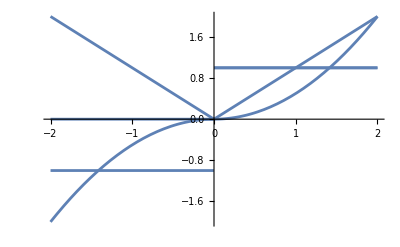

```mathematica
Show[plot4,plot5,plot6,plot7]
```